```mathematica
Play[Sin[5000x],{x,0,1}]
```

-Graphics-

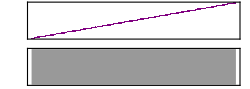

```mathematica
Sound[SoundNote/@{"C-1","D-1","E-1","F-1","G-1","A-1","B-1","C0","D0","E0","F0","G0","A0","B0","C1","D1","E1","F1","G1","A1","B1","C2","D2","E2","F2","G2","A2","B2","C3","D3","E3","F3","G3","A3","B3","C4","D4","E4","F4","G4","A4","B4","C5","D5","E5","F5","G5","A5","B5","C6","D6","E6","F6","G6","A6","B6","C7","D7","E7","F7","G7","A7","B7","C8","D8","E8","F8","G8","A8","B8","C9","D9","E9","F9","G9"},3]
```

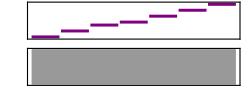

```mathematica
Sound[SoundNote/@{"C#","D#","E#","F#","G#","A#","B#"},0.5]
```

```mathematica
Play[Sin[2^x],{x,0,20}]
```

-Graphics-

```mathematica
Dynamic[If[a!=Date[],a=Date[]]]
```

```mathematica
b=Date[];
b[[4]]
```

8

```mathematica
With[{p=RandomReal[10,{100,2}]},Graphics[{Line[p[[Last[FindShortestTour[p]]]]],PointSize[Large],Red,Point[p]}]]
```

```mathematica
With[{p=RandomReal[15,{50,3}]},Graphics3D[{Thick,Line[p[[Last[FindShortestTour[p]]]]],Opacity[.3],Sphere/@p}]]
```

```mathematica
Graphics[{Gray,CountryData[#,{"SchematicPolygon","Equirectangular"}]&/@CountryData["Europe"],Thick,Red,Line[#[[Last[FindShortestTour[#]]]]&[Reverse[CountryData[#,"CenterCoordinates"]]&/@CountryData["Europe"]]]}]
```

```mathematica
Text[#[[Last[FindShortestTour[#,DistanceFunction->EditDistance]]]]&[CountryData[]]]
```

```mathematica
FindMinimum[{Total[Array[x,100]],Join[Thread[RandomInteger[{-100,100},{100,100}].Array[x,100]>1],Thread[Array[x,100]>0],{Array[x,100]∈Integers}]},Array[x,100]]
```

```mathematica
Table[With[{f=Sin[x+Cos[y]],cons=x^2<y^3+5&&y^2<x^3+u},Show[ContourPlot[f,{x,-2,3},{y,-2,3},RegionFunction->Function@@{{x,y},cons},ColorFunction->"ThermometerColors"],Graphics[{Blue,Disk[{x,y}/.Last[FindMinimum[{f,cons},{x,y}]],.2]}]]],{u,-1,2}]
```

```mathematica
cloud=(# {1,.5})&/@RandomReal[NormalDistribution[],{200,2}];
```

```mathematica
sol=FindMinimum[{r^4/(t^2 s^2),Map[t^2 (#[[1]]-a)^2+s^2 (#[[2]]-b)^2<r^2&,cloud]},{r,a,b,t,s}]
```

{27.8142,{r→2.47537,a→-0.525741,b→0.123497,t→0.766091,s→1.51658}}

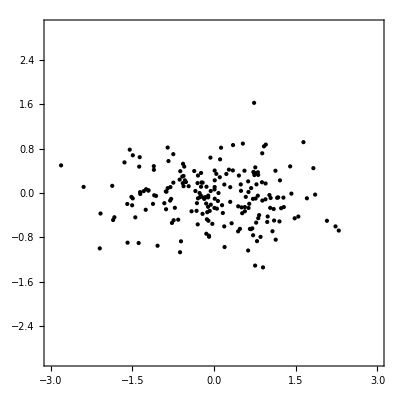

```mathematica
RegionPlot[((t^2(x-a))^2+(s^2(y-b))^2<r^2)/.Last[sol],{x,-3,3},{y,-3,3},Epilog->Point[cloud]]
```

```mathematica
DictionaryLookup["r"~~___~~"r"]
```

{racegoer,racer,racier,racketeer,raconteur,radar,radder,radiator,radiographer,radiometer,rafter,raggeder,raggedier,raider,railroader,rainier,rainmaker,rainwater,raiser,rambler,rancher,rancor,randier,rangefinder,ranger,rangier,ranker,ransomer,ranter,raper,rapider,rapier,rapper,rapporteur,raptor,rarer,rasher,rasper,raspier,raster,ratepayer,rater,rather,rathskeller,ratifier,ratter,rattier,rattler,rattlier,raunchier,ravager,raver,ravisher,rawer,razor,reactor,reader,readier,realer,reamer,reaper,reappear,rear,reasoner,receiver,recenter,receptor,recharger,recharter,reciter,reckoner,reclaimer,recliner,recognizer,recolor,reconnoiter,reconquer,reconsider,recorder,recover,recruiter,rectangular,rectifier,rectilinear,rector,recur,redactor,redder,redeemer,redefiner,redeliver,rediscover,reducer,reedier,reefer,reenter,refer,referencer,referrer,refiner,reflector,reformer,refresher,refrigerator,refuter,regather,register,registrar,regular,regulator,rehear,reindeer,rejigger,rejoinder,relater,relaxer,reliever,remainder,remaster,remember,reminder,remoter,remover,render,reneger,renovator,renter,renumber,reoccur,reorder,repair,repairer,repaper,repeater,replicator,replier,reporter,reproducer,repudiator,requester,requiter,rescuer,researcher,reseller,reservoir,resister,resistor,resoluter,resolver,resonator,respecter,respirator,responder,restaurateur,restfuller,restorer,restrainer,resuscitator,retailer,retainer,retarder,reticular,retriever,returner,reupholster,reveler,revenuer,reverser,reviewer,reviler,reviser,reviver,revoker,revolver,rheumier,rhymer,rhymester,ribber,ricer,richer,ricketier,rider,ridgier,rifer,rifler,rigger,righter,rigor,ringer,ringleader,ringmaster,rioter,riper,ripper,ripplier,riser,riskier,ritzier,river,riveter,roadrunner,roadster,roamer,roar,roarer,roaster,robber,robuster,rocker,rockier,roger,roister,roisterer,roller,rollover,romancer,romper,roofer,rookier,roomer,roomier,rooster,rooter,roper,rosewater,rosier,roster,rotor,rototiller,rottener,rotter,rottweiler,rougher,rounder,router,rover,rowdier,rower,rubber,rubberier,rubbernecker,rubier,rudder,ruddier,ruder,rufflier,ruggeder,rugger,ruler,rummer,rumor,rumormonger,rumplier,runner,runnier,runtier,rusher,rushier,rustier,rustler,ruttier}

```mathematica
WordData["break"]
```

{{break,Noun,Flight},{break,Noun,OpenFrame},{break,Noun,Dash},{break,Noun,ChangeOfIntegrity},{break,Noun,Holdup},{break,Noun,BreakOfServe},{break,Noun,Shot},{break,Noun,Pause},{break,Noun,Modification},{break,Noun,Breach},{break,Noun,Fortuity},{break,Noun,Breakup},{break,Noun,Occurrent},{break,Noun,Crevice},{break,Noun,Hurt},{break,Noun,Interval},{break,Verb,Weaken},{break,Verb,Diminish},{break,Verb,Injure},{break,Verb,Fall},{break,Verb,Domesticate},{break,Verb,Change},{break,Verb,Turn},{break,Verb,Damage},{break,Verb,ChangeIntegrity},{break,Verb,Divide},{break,Verb,Check},{break,Verb,Develop},{break,Verb,BreakOff},{break,Verb,Interrupt},{break,Verb,Deaden},{break,Verb,BreakDown},{break,Verb,ChangeVoice},{break,Verb,Go},{break,Verb,Lick},{break,Verb,Destroy},{break,Verb,Diphthongize},{break,Verb,Disrupt},{break,Verb,Pause},{break,Verb,Tell},{break,Verb,GetOut},{break,Verb,Outstrip},{break,Verb,Penetrate},{break,Verb,BecomePunctured},{break,Verb,Detach},{break,Verb,Crumble},{break,Verb,Bust},{break,Verb,Disunite},{break,Verb,Shoot},{break,Verb,Modify},{break,Verb,Exchange},{break,Verb,ExpressFeelings},{break,Verb,TripTheLightFantasticToe},{break,Verb,GiveWay},{break,Verb,Founder},{break,Verb,Appear},{break,Verb,Scatter},{break,Verb,TakeFlight},{break,Verb,GetAway},{break,Verb,ChangeDirection},{break,Verb,Impoverish},{break,Verb,Designate},{break,Verb,Split},{break,Verb,Invalidate},{break,Verb,BreakAway},{break,Verb,Ruin},{break,Verb,Disrespect},{break,Verb,Trespass},{break,Verb,ComeAbout},{break,Verb,Emerge},{break,Verb,Violate},{break,Verb,Quit},{break,Verb,GiveUpHabit},{break,Verb,Vary},{break,Verb,Finish},{break,Interjection}}

```mathematica
Import["http://www.forbes.com/2003/09/17/rich400land.html","Data"]
```

{ Home > Lists > Forbes 400 ,{{ ,{{{{The Richest,Media Moguls,Realtors,Landowners},{Financiers,Oil Barons,Gamblers,New Members},{Techies,Near Misses,Dropoffs,Died},{ , > }}, or },{{ the,category Net Worth ($millions) Age Place of Residence Marital Status Industry Magazine Section},{ is,selection (Please select a category above)}, and,{ the,category Net Worth ($millions) Age Place of Residence Marital Status Industry Magazine Section},{ is,selection (Please select a category above), > }}}},{ Senior Editor Peter Newcomb discusses this year's list , Donal Trump: The Kid Stays In The Picture , Hometowns Of The Richest , The Richest And The States , Hangdan , Which Billionaire Are You? ,{How much money does a person need to be considered truly wealthy?,$1 - 5 million,$5 - 10 million,$10 - 50 million,$50 - 100 million,$100 - 200 million,$200 - 500 million,$600 million (this year's list's cut-off level),$1 billion,True wealth is not measured by dollar signs,I don't know, },{{ , Download the List (PDA) }, , Peopletracker , }}},1 of 1 , , ,{Delivered By ,Tested By ,Market Data By ,Market Data By ,Market Data By ,American History ,Luxury Cars }}

```mathematica
Row[Take[Framed[Column[#]]&/@FindClusters[DictionaryLookup["ac"~~__],100],30]]
```

acacia
acaciasacademe
academyacademiaacademic
academics
academiesacademical
academically
academician
academiciansacanthus
accord
accords
across
actor
actorsacanthuses
access
accusal
accused
accuser
accusers
accusesaccede
acceded
accedes
acreageaccedingaccelerate
accelerated
accelerates
accelerator
accelerators
accelerometer
accelerometersaccelerating
acceleration
accelerationsaccent
acceptaccented
acceptedaccenting
accountingaccents
acceptsaccentualaccentuate
accentuated
accentuates
accentuating
acupunctureaccentuation
acceptation
acceptationsacceptability
accountabilityacceptable
acceptably
acceptance
acceptances
accountableacceptablenessacceptingacceptor
acceptorsaccessed
accessioned
accessorized
accostedaccesses
accessories
accessorizes
actressesaccessibility
accessible
accessibly
accessoryaccessing
accession
accessioning
accessions
accessorize
accessorizingaccidence
accident
accidents
acridestaccidental
accidentally
accidentalsacclaim
acclaims
acyclovir

```mathematica
ListLogLogPlot[Reverse[Sort[Last/@Tally[ExampleData[{"Text","OriginOfSpecies"},"Words"]]]],Joined->True,Filling->Axis,PlotRange->All,Frame->True]
```

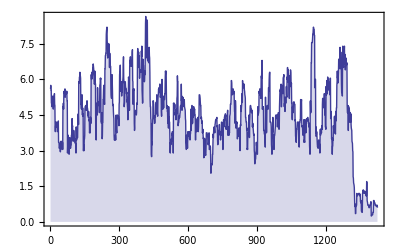

```mathematica
ListLinePlot[MovingAverage[Length[WordData[ToLowerCase[#]]]&/@Flatten[StringCases[ExampleData[{"Text","DeclarationOfIndependence"},"Words"],LetterCharacter..]],20],Filling->Axis,PlotRange->{0,All},Frame->True]
```

```mathematica
RegionPlot[x^2-x y+y^6>2,{x,-2,2},{y,-2,2}]
```

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2},Mesh->All]
```

```mathematica
RegionPlot3D[x^2+y^3-z^2>0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

```mathematica
ContourPlot[Sin[x+Cos[y]],{x,-3,3},{y,-3,3},RegionFunction->(1<#1^2+#2^2<9&),ColorFunction->"BlueGreenYellow",BoundaryStyle->Red]
```

```mathematica
data=Table[RandomReal[{-4,4},{2}]->i,{i,40}];
```

```mathematica
nf=Nearest[data,DistanceFunction->(Norm[#1-#2,Infinity]&)];
```

```mathematica
ContourPlot[First[nf[{x,y}]],{x,-5,5},{y,-5,5},PlotPoints->50,Contours->Range[1/2,40],ColorFunction->"Pastel",Epilog->{Red,PointSize[Large],Point[First/@data]}]
```

-Graphics-

```mathematica
Simplify[Apply[Composition,Table[Composition[RotationTransform[Subscript[θ,i]],TranslationTransform[{Subscript[a,i],0}]],{i,10}]][{x,y}]]//TraditionalForm
```

{a_10 cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10)+a_1 cos(θ_1)+a_2 cos(θ_1+θ_2)+a_3 cos(θ_1+θ_2+θ_3)+a_4 cos(θ_1+θ_2+θ_3+θ_4)+a_5 cos(θ_1+θ_2+θ_3+θ_4+θ_5)+a_6 cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6)+a_7 cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7)+a_8 cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8)+a_9 cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9)+x cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10)-y sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10),a_1 sin(θ_1)+a_2 sin(θ_1+θ_2)+a_3 sin(θ_1+θ_2+θ_3)+a_4 sin(θ_1+θ_2+θ_3+θ_4)+a_5 sin(θ_1+θ_2+θ_3+θ_4+θ_5)+a_6 sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6)+a_7 sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7)+a_8 sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8)+a_9 sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9)+a_10 sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10)+x sin(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10)+y cos(θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7+θ_8+θ_9+θ_10)}

```mathematica
GraphicsGrid[Partition[PolyhedronData/@PolyhedronData["Uniform"],4]]
```

```mathematica
ParametricPlot3D[{1.13^v Cos[v] (1+Cos[u]),-1.13^v Sin[v] (1+Cos[u]),-1.4 1.13^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},PlotRange->All,MeshFunctions->{(#1^2+#2^2-5&)},Mesh->{{0}},MeshShading->{Opacity[.4,Yellow],Red},MaxRecursion->4,Axes->None]
```

```mathematica
Sound
```

```mathematica
note[b_,x0_,t_,v_]:=Module[{a=b},Which[x0=="1",AppendTo[a,SoundNote["C",t,SoundVolume->v]],x0=="2",AppendTo[a,SoundNote["D",t,SoundVolume->v]],x0=="3",AppendTo[a,SoundNote["E",t,SoundVolume->v]],x0=="4",AppendTo[a,SoundNote["F",t,SoundVolume->v]],x0=="5",AppendTo[a,SoundNote["G",t,SoundVolume->v]],x0=="6",AppendTo[a,SoundNote["A",t,SoundVolume->v]],x0=="7",AppendTo[a,SoundNote["B",t,SoundVolume->v]],x0=="0",AppendTo[a,SoundNote[None,t,SoundVolume->v]],x0=="-",a[[-1,2]]*=2,x0=="_",a[[-1,2]]/=2,x0=="*",a[[-1,2]]*=1.5,x0=="t",a[[-1,2]]/=3,x0=="%",a[[-1,2]]/=5,x0==".",a[[-1,1]]=If[NumberQ@ToExpression[StringTake[a[[-1,1]],-1]],StringReplacePart[a[[-1,1]],ToString[ToExpression[StringTake[a[[-1,1]],-1]]-1],-1],StringInsert[a[[-1,1]],"3",-1]],x0=="'",a[[-1,1]]=If[NumberQ@ToExpression[StringTake[a[[-1,1]],-1]],StringReplacePart[a[[-1,1]],ToString[ToExpression[StringTake[a[[-1,1]],-1]]+1],-1],StringInsert[a[[-1,1]],"5",-1]],x0=="#",a[[-1,1]]=StringInsert[a[[-1,1]],"#",-1],x0=="b",a[[-1,1]]=StringInsert[a[[-1,1]],"b",-1]];a];

noteh[b_,x0_]:=Module[{h=b},Which[x0=="1",AppendTo[h,"C"],x0=="2",AppendTo[h,"D"],x0=="3",AppendTo[h,"E"],x0=="4",AppendTo[h,"F"],x0=="5",AppendTo[h,"G"],x0=="6",AppendTo[h,"A"],x0=="7",AppendTo[h,"B"],x0==".",h[[-1]]=If[NumberQ@ToExpression[StringTake[h[[-1]],-1]],StringReplacePart[h[[-1]],ToString[ToExpression[StringTake[h[[-1]],-1]]-1],-1],StringInsert[h[[-1]],"3",-1]],x0=="'",h[[-1]]=If[NumberQ@ToExpression[StringTake[h[[-1]],-1]],StringReplacePart[h[[-1]],ToString[ToExpression[StringTake[h[[-1]],-1]]+1],-1],StringInsert[h[[-1]],"5",-1]],x0=="#",h[[-1]]=StringInsert[h[[-1]],"#",-1],x0=="b",h[[-1]]=StringInsert[h[[-1]],"b",-1]];h];

mf[s_,t_,x_]:=Module[{lh=StringLength[x],xx=x,a={},v=1,par=False,h={},i,x0},For[i=1,i≤lh,i++,x0=StringTake[xx,1];
If[par,If[x0==")",AppendTo[a,SoundNote[h,t,SoundVolume->v]];par=False;
h={},h=noteh[h,x0]],If[x0=="(",par=True,v=Which[x0=="p",0.5,x0=="P",0.2,x0=="m",0.8,x0=="f",1,True,v];a=note[a,x0,t,v]]];
xx=StringDrop[xx,1]];
Sound[Prepend[a,s],{0,Plus@@(#[[2]]&/@a)}]];

(*函数mf[s,t,x]，s，t，x分别为乐器类型、时长单位（秒）、乐谱*)

m[t_,x_]:=mf["Piano",t,x];

(*函数m[t,x]，t，x分别为时长单位（秒）、乐谱，乐器类型默认为钢琴*)

ms[s_,x_]:=mf[s,0.5,x];

(*函数ms[s,x]，s，x分别为乐器类型、乐谱，时长单位默认为0 .5秒*)

m0[x_]:=m[0.5,x];

(*函数m0[x]，x为乐谱，乐器类型默认为钢琴，时长单位默认为0 .5秒*)
```

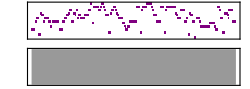

```mathematica
m[0.5,"5.-12|3.4_31|2-16.|1--|5.-12|33_4_51|43_52_3_|3_2_2-|3-57|7.6_6-|55_6_76_5_|3-|4.4_56|54_3_2-|7.7._6._5.6.|1-|1-6-|4.5_6-77_7_76_5_|3-|1-6-|4.5_6-|66_6_64_3_|2-|5-12|3.4_31_1_|2.2_22_1_|6.6.--7.-7.6._|5.652_2_|4.4_43_2_|5-|1-"]
```